```mathematica
NorthEast[n_]:=(n-2)^2+n-1;
NorthWest[n_]:=(n-2)^2+2n-2;
SouthWest[n_]:=(n-2)^2+3n-3;
```

```mathematica
countPrimes[n_]:= (
result=0;
For[i=1,i≤ n,i=i+2,
result=result+If[PrimeQ[NorthEast[i]],1,0]+If[PrimeQ[NorthWest[i]],1,0]+
If[PrimeQ[SouthWest[i]],1,0]
];result);
```

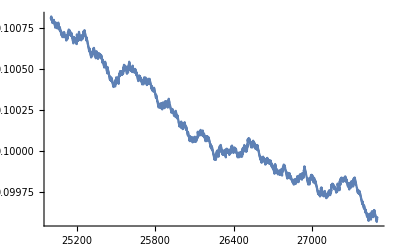

```mathematica
Plot[countPrimes[n]/(4 Floor[n/2]+1),{n,25000,27500}]
```

```mathematica
n=26241;
countPrimes[n]/(4 Floor[n/2]+1)<1/10
```

True

```mathematica
countPrimes[25000]/(4 Floor[25000/2]+1)
```

5041/50001